# σ_T with Eikonal Corrections

## Micah Buuck

7/23/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=(2/3*.535)^(-1/2) (*Femto Meter*);
V0=-50 (*Mega ElectronVolt*);
V[r_]:=V0*E^(-r^2/R^2);
```

The value for R is from the Schwaller paper. I had to make up numbers for V0 and a. What would probably have been better would be to make the potential a Gaussian, since I think that is more similar to what they have done in the paper.

### Plot for potential

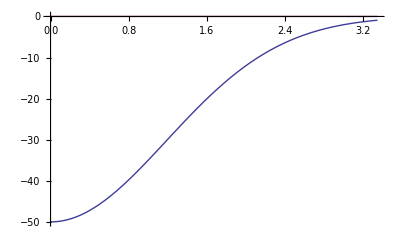

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Partial Wave Expansion

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

```mathematica
σT[k_]:=10*4*Pi/k*Im[f[k,0]];
```

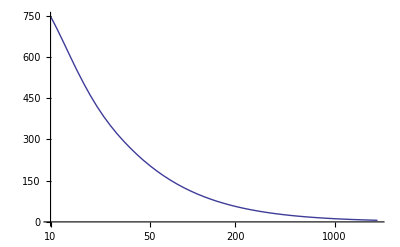

```mathematica
p=LogLinearPlot[σT[Sqrt[2*m*En]/ℏc],{En,10,2000}]
```

```mathematica
1400^2/(2*938.)
```

1044.78

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

```mathematica
σ0T[k_]:=10*4*Pi/k*Im[Eif0[k,0]];
```

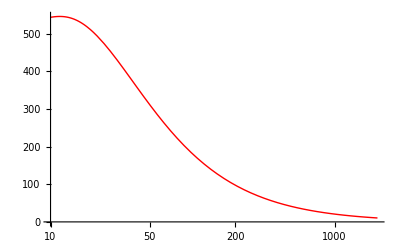

```mathematica
p0=LogLinearPlot[σ0T[Sqrt[2*m*En]/ℏc],{En,10,2000},PlotStyle->Red]
```

## Add in Eikonal Corrections

### First order correction

Below are parameters used by Wallace in his treatment of this:

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
σ1T[k_]:=10*4*Pi/k*Im[Eif1[k,0]];
```

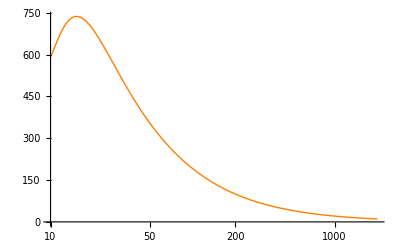

```mathematica
p1=LogLinearPlot[σ1T[Sqrt[2*m*En]/ℏc],{En,10,2000},PlotStyle->Orange]
```

### Second order correction

```mathematica
τ2[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0[k,b],b]^3/(24*k^2);
ω2[k_,b_]=D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2);
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
σ2T[k_]:=10*4*Pi/k*Im[Eif2[k,0]];
```

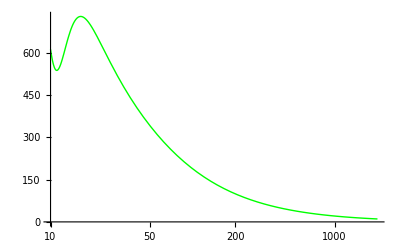

```mathematica
p2=LogLinearPlot[σ2T[Sqrt[2*m*En]/ℏc],{En,10,2000},PlotStyle->Green]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
σ3T[k_]:=10*4*Pi/k*Im[Eif3[k,0]];
```

```mathematica
σ3T[Sqrt[2*m*10]/ℏc]
```

45590.1

This seems way too high. I think something is probably going wrong with NIntegrate.

```mathematica
Table[σ3T[Sqrt[2*m*En]/ℏc],{En,10,2000,100}]
```

$Aborted

```mathematica
p3=LogLinearPlot[σ3T[Sqrt[2*m*En]/ℏc],{En,10,2000},PlotStyle->Purple]
```

$Aborted

These took too long to evaluate.

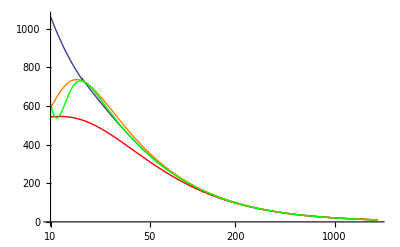

```mathematica
Show[p,p0,p1,p2]
```

Blue: partial wave
Red: 0th order eikonal
Orange: 1st order eikonal
Greed: 2nd order eikonal

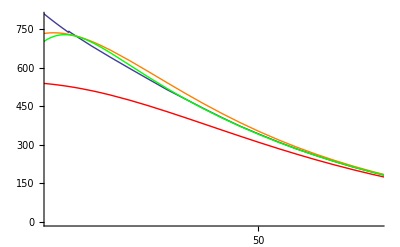

```mathematica
Show[p,p0,p1,p2,PlotRange->{{Log[15],Log[100]},{0,800}}]
```

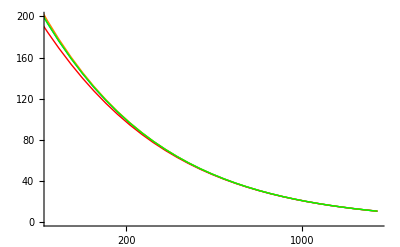

```mathematica
Show[p,p0,p1,p2,PlotRange->{{Log[100],Log[2000]},{0,200}}]
```